```mathematica
ComplexPlot3D[Gamma[z],{z,-4-4I,4+4I}]
```

-Graphics3D-

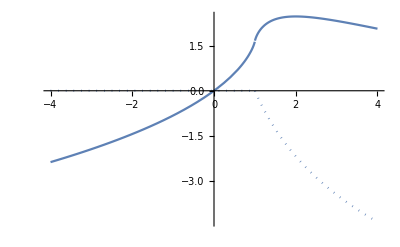

```mathematica
ReImPlot[PolyLog[2,x],{x,-4,4}]
```

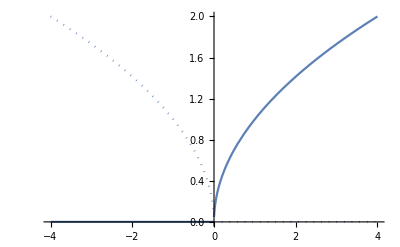

```mathematica
ReImPlot[Sqrt[x], {x, -4,4}]
```

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
Solve[x^5+6 x+1==0,x]
```

{{x→Root-0.167Root[1+6 #1+#1^5&,1]-0.16664524696557537},{x→Root-1.06-1.11 ⅈRoot[1+6 #1+#1^5&,2]-1.063086977075791},{x→Root-1.06+1.11 ⅈRoot[1+6 #1+#1^5&,3]-1.063086977075791},{x→Root1.15-1.11 ⅈRoot[1+6 #1+#1^5&,4]1.1464096005585789},{x→Root1.15+1.11 ⅈRoot[1+6 #1+#1^5&,5]1.1464096005585789}}

```mathematica
Integrate[x^3,x,GeneratedParameters->C]
```

x^4/4+C[1]

```mathematica
∫Sqrt[Sqrt[x]+Sqrt[2 x+2 Sqrt[x]+1]+1] ⅆx
```

(2 √(1+√x+√(1+2 √x+2 x)) (2+√x+6 x^(3/2)+(-2+√x) √(1+2 √x+2 x)))/(15 √x)

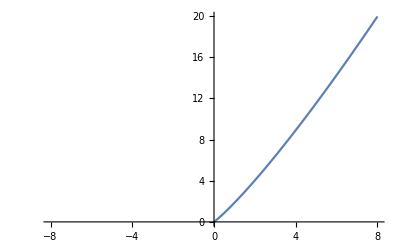

```mathematica
Plot[(2 √(1+√x+√(1+2 √x+2 x)) (2+√x+6 x^(3/2)+(-2+√x) √(1+2 √x+2 x)))/(15 √x),{x,-8,8}]
```

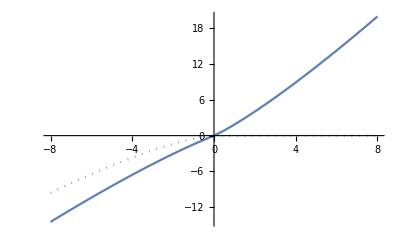

```mathematica
ReImPlot[(2 √(1+√x+√(1+2 √x+2 x)) (2+√x+6 x^(3/2)+(-2+√x) √(1+2 √x+2 x)))/(15 √x),{x,-8,8}]
```

```mathematica
AsymptoticSolve[x y^4-(x+1) y^2+x==1,y,{x,0,3},Reals]
```

{{y→-1/(√x)-√x+2 x^(3/2)},{y→1/(√x)+√x-2 x^(3/2)}}

```mathematica
Graphics3D[RandomPolygon[20]]
```

-Graphics3D-

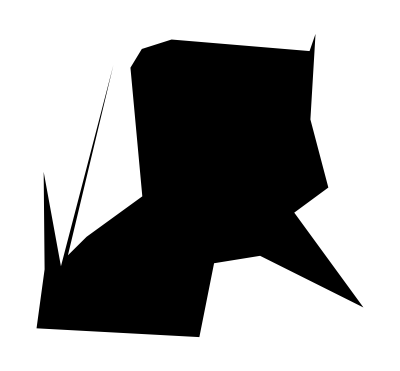

```mathematica
Graphics[RandomPolygon[20]]
```

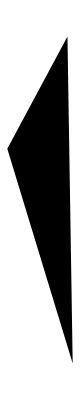
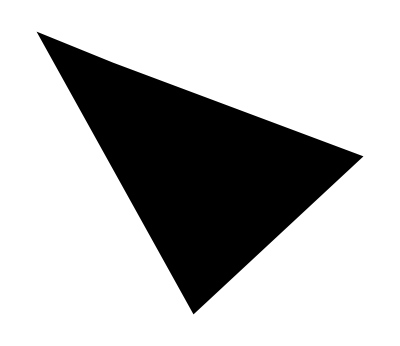
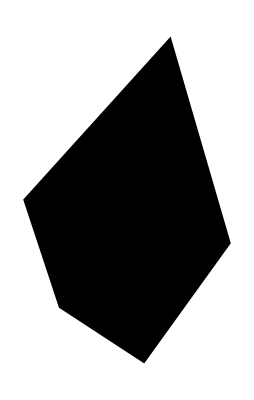
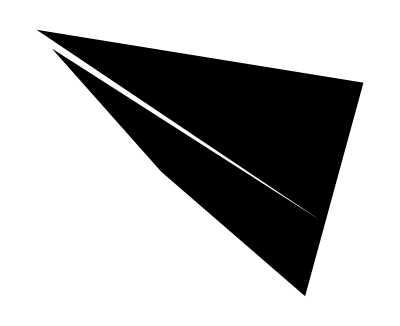
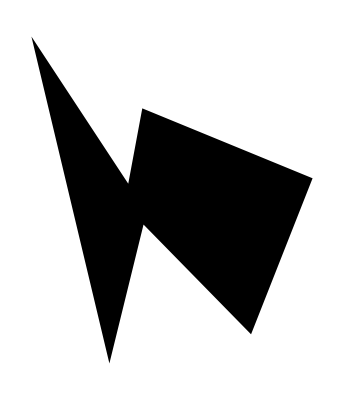
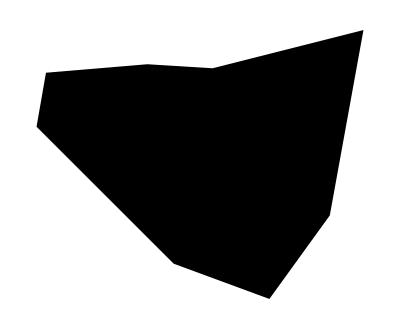
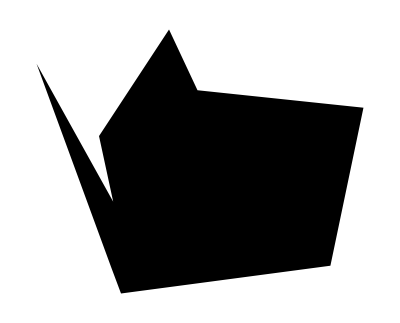
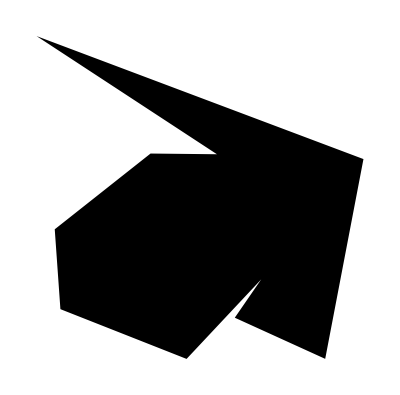
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics@RandomPolygon@i,{i,1,50}]
```

```mathematica
Graphics3D[RandomPolygon[3->{"Convex",10},5]]
```

-Graphics3D-

Area::reg: RandomPolygon[1] is not a correctly specified region.

Area::reg: RandomPolygon[2] is not a correctly specified region.

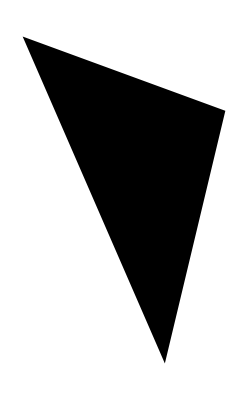
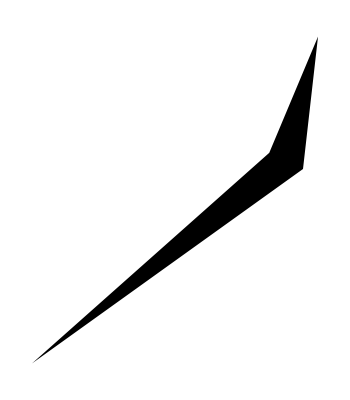
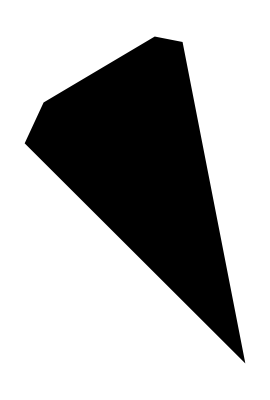
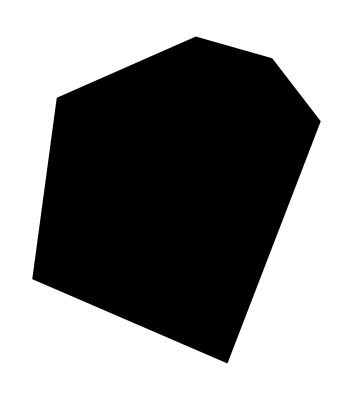
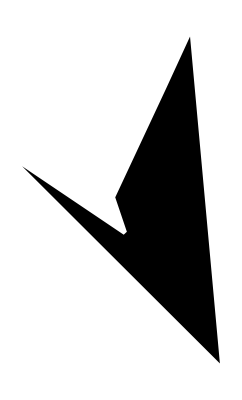
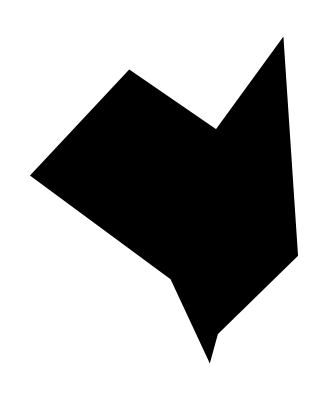
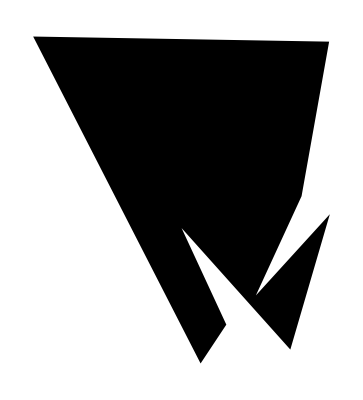
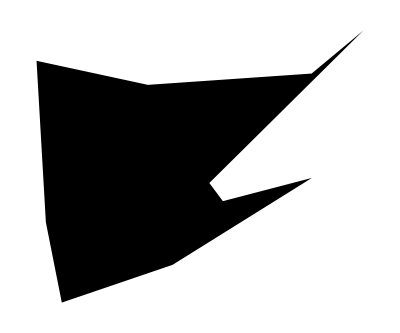
{{-Graphics-,Area[RandomPolygon[1]]},{-Graphics-,Area[RandomPolygon[2]]},{-Graphics-,0.220758},{-Graphics-,0.0460406},{-Graphics-,0.221051},{-Graphics-,0.289723},{-Graphics-,0.149949},{-Graphics-,0.372749},{-Graphics-,0.44412},{-Graphics-,0.376355},{-Graphics-,0.440881},{-Graphics-,0.374672},{-Graphics-,0.286527},{-Graphics-,0.251861},{-Graphics-,0.413906},{-Graphics-,0.355226},{-Graphics-,0.458757},{-Graphics-,0.623631},{-Graphics-,0.340903},{-Graphics-,0.536723},{-Graphics-,0.406003},{-Graphics-,0.362182},{-Graphics-,0.540282},{-Graphics-,0.367926},{-Graphics-,0.458253},{-Graphics-,0.548116},{-Graphics-,0.433358},{-Graphics-,0.419686},{-Graphics-,0.432034},{-Graphics-,0.354033},{-Graphics-,0.395488},{-Graphics-,0.39021},{-Graphics-,0.513723},{-Graphics-,0.501733},{-Graphics-,0.388329},{-Graphics-,0.398408},{-Graphics-,0.360903},{-Graphics-,0.457187},{-Graphics-,0.375859},{-Graphics-,0.41003},{-Graphics-,0.439505},{-Graphics-,0.388663},{-Graphics-,0.418076},{-Graphics-,0.480046},{-Graphics-,0.532407},{-Graphics-,0.534033},{-Graphics-,0.553565},{-Graphics-,0.483328},{-Graphics-,0.375511},{-Graphics-,0.444754}}

```mathematica
Table[With[{poly=RandomPolygon@i},
{Graphics@poly,Area@poly}],{i,1,50}]
```

```mathematica
Graphics3D[Dodecahedron[]]
```

-Graphics3D-

```mathematica
Graphics@Cube[]
```

-Graphics-

```mathematica
Graphics3D@Cube[]
```

-Graphics3D-

```mathematica
Dodecahedron[
```

```mathematica
Graphics3D[BeveledPolyhedron[Dodecahedron[],1]]
```

-Graphics3D-

```mathematica
Graphics3D[AugmentedPolyhedron[PolyhedronData["Spikey","Polyhedron"],2]]
```

-Graphics3D-

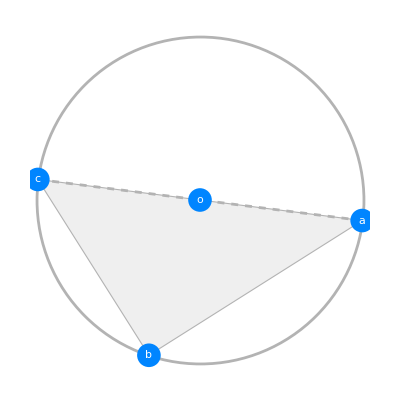
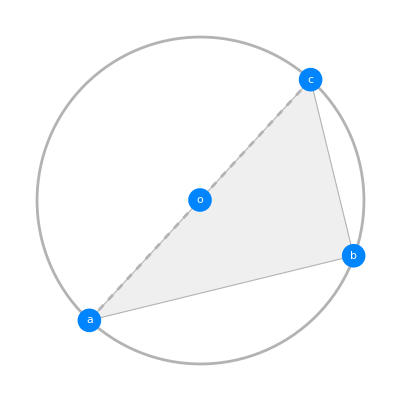
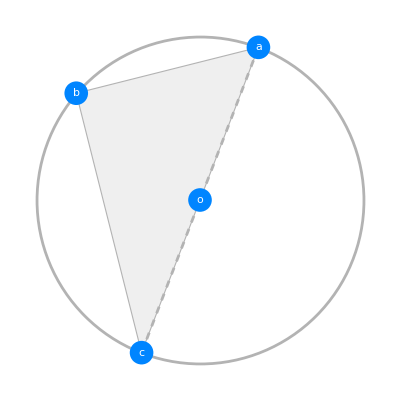
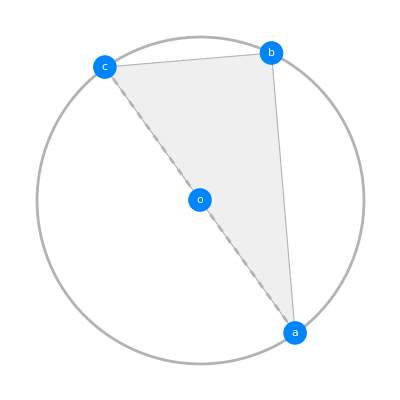
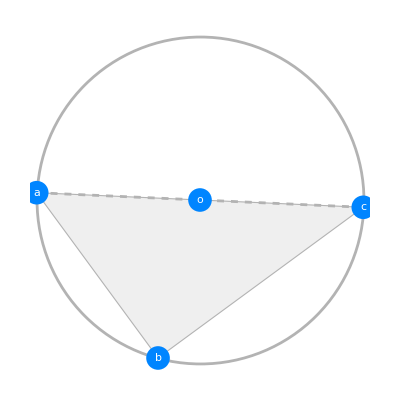
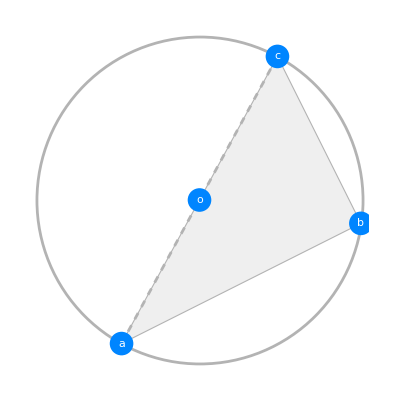
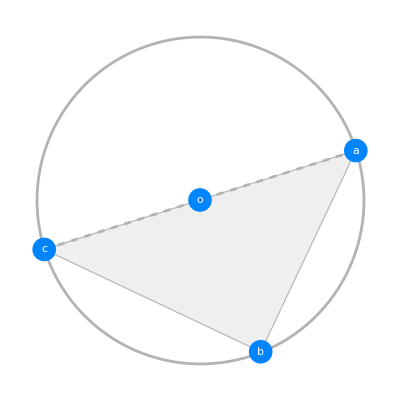
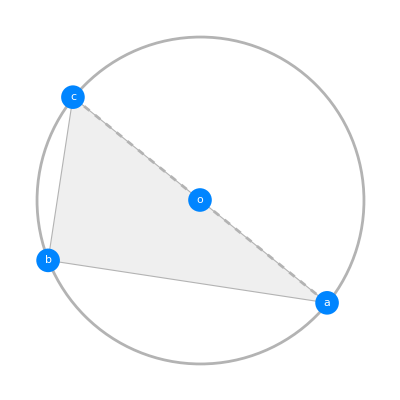

```mathematica
Table[RandomInstance[GeometricScene[{a,b,c,o},{Triangle[{a,b,c}],CircleThrough[{a,b,c},o],o==Midpoint[{a,c}]}]], {i, 1, 10}]
```

```mathematica
FindGeometricConjectures[GeometricScene[{a,b,c,o},{Triangle[{a,b,c}],CircleThrough[{a,b,c},o],o==Midpoint[{a,c}]}]]
```

```mathematica
RandomInstance[GeometricScene[{"C","B","A","C'","B'","A'","Oc","Ob","Oa"},{Triangle[{"C","B","A"}],TC==Triangle[{"A","B","C'"}],TB==Triangle[{"C","A","B'"}],TA==Triangle[{"B","C","A'"}],GeometricAssertion[{TC,TB,TA},"Regular"],"Oc"==TriangleCenter[TC,"Centroid"],"Ob"==TriangleCenter[TB,"Centroid"],"Oa"==TriangleCenter[TA,"Centroid"],Triangle[{"Oc","Ob","Oa"}]}]]
```

-Graphics-

```mathematica
AxiomaticTheory["WolframAxioms"]
```

{∀_{a,b,c}((b·c)·a)·(b·((b·a)·b))==a}

```mathematica
And[And[And[b,c],a],And[b,And[And[b,a],b]]]
```

b&&c&&a&&b&&b&&a&&b

```mathematica
TableForm[BooleanTable[{a,b,c,b&&c&&a&&b&&b&&a&&b},{a,b,c}],TableHeadings->{None,{a,b,c,b&&c&&a&&b&&b&&a&&b}}]
```

a | b | c | b&&c&&a&&b&&b&&a&&b
True | True | True | True
True | True | False | False
True | False | True | False
True | False | False | False
False | True | True | False
False | True | False | False
False | False | True | False
False | False | False | False

```mathematica
FindEquationalProof[p·q==q·p,AxiomaticTheory["WolframAxioms"]]
```

ProofObject[…]

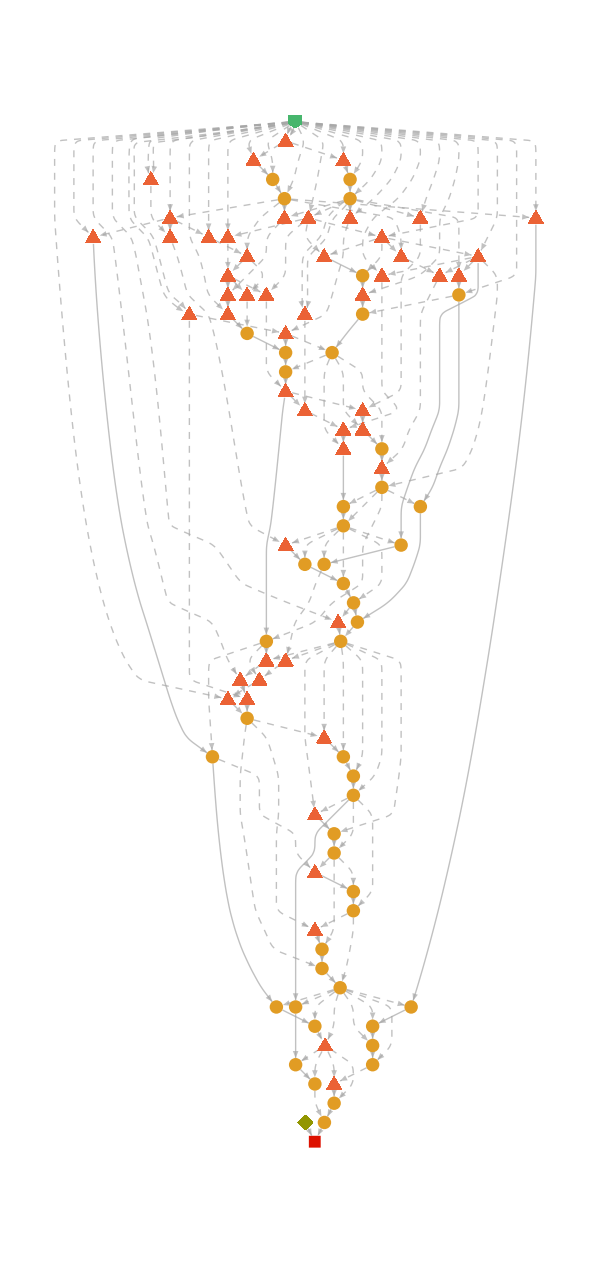

```mathematica
Out[27]["ProofGraph"]
```

```mathematica
And[And[And[b,c],a],And[b,And[And[b,a],b]]]==a
```

(b&&c&&a&&b&&b&&a&&b)==a

```mathematica
Reduce[(b&&c&&a&&b&&b&&a&&b)==a]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(b&&c&&a&&b&&b&&a&&b)==a]

```mathematica
AxiomaticTheory[{"WolframAxioms",<|"Nand"->f|>}]
```

{∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a}

```mathematica
Resolve[{∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a}]
```

∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a

```mathematica
Resolve[∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a]
```

∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a

```mathematica
Resolve[∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a]
```

∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a

```mathematica
Solve[∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a,{f[b,a],f[b,c]}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[∀_{a,b,c}f[f[f[b,c],a],f[b,f[f[b,a],b]]]==a,{f[b,a],f[b,c]}]

```mathematica
AxiomaticTheory["GroupAxioms"]
```

{∀_{a,b,c}a⊗(b⊗c)==(a⊗b)⊗c,∀_a a⊗OverTilde[1]==a,∀_a a⊗ā==OverTilde[1]}

```mathematica
AxiomaticTheory["GroupAxioms","Operators"]
```

<|Multiplication→CircleTimes,Inverse→OverBar,Identity→OverTilde[1]|>

```mathematica
PDF[NormalDistribution[0,1]]
```

Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

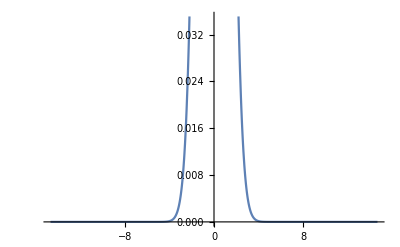

```mathematica
Plot[Function[x,(ⅇ^(-x^2/2))/(√(2 π))][x],{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
Sum[2^n n!,n]
```

DifferenceRoot[Function[{y,n},{(2+2 n) y[n]+(-3-2 n) y[1+n]+y[2+n]==0,y[0]==0,y[1]==1}]][n]

```mathematica
Entity["Surface","Torus"][EntityProperty["Surface","AlgebraicEquation"]]
```

Function[{a,c},Function[{x,y,z},a^4-2 a^2 c^2+c^4-2 a^2 x^2-2 c^2 x^2+x^4-2 a^2 y^2-2 c^2 y^2+2 x^2 y^2+y^4-2 a^2 z^2+2 c^2 z^2+2 x^2 z^2+2 y^2 z^2+z^4]]

```mathematica
SurfaceData[Entity["Surface","Torus"],"ChristoffelSymbolOfTheSecondKind"]
```

Function[{a,c},Function[{u,v},{{{0,-(a Sin[v])/(c+a Cos[v])},{-(a Sin[v])/(c+a Cos[v]),0}},{{((c+a Cos[v]) Sin[v])/a,0},{0,0}}}]]

```mathematica
AxiomaticTheory["BooleanAxioms"]
```

{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}

```mathematica
Groupings[{a,b},%]
```

Groupings::arity: Invalid arity specification ∀_{a,b}a⊗b==b⊗a.

Groupings[{a,b},{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}]

```mathematica
AxiomaticTheory["BooleanAxioms","OperatorArities"]
```

{CircleTimes→2,CirclePlus→2,OverBar→1}

```mathematica
Groupings[{a,b},%]
```

{ā⊗b,a⊗b̄,OverBar[a⊗b],OverBar[ā]⊗b,a⊗OverBar[b̄],ā⊗b̄,OverBar[ā⊗b],OverBar[a⊗b̄],OverBar[OverBar[a⊗b]],ā⊕b,a⊕b̄,OverBar[a⊕b],OverBar[ā]⊕b,a⊕OverBar[b̄],ā⊕b̄,OverBar[ā⊕b],OverBar[a⊕b̄],OverBar[OverBar[a⊕b]]}

```mathematica
Groupings[{a,b},{CircleTimes->2,CirclePlus->2,OverBar->1}]
```

{ā⊗b,a⊗b̄,OverBar[a⊗b],OverBar[ā]⊗b,a⊗OverBar[b̄],ā⊗b̄,OverBar[ā⊗b],OverBar[a⊗b̄],OverBar[OverBar[a⊗b]],ā⊕b,a⊕b̄,OverBar[a⊕b],OverBar[ā]⊕b,a⊕OverBar[b̄],ā⊕b̄,OverBar[ā⊕b],OverBar[a⊕b̄],OverBar[OverBar[a⊕b]]}

```mathematica
Groupings[Range[3], {Plus->2}]
```

{6,6}

```mathematica
Groupings[{a,b,c}, {Plus->2}]
```

{a+b+c,a+b+c}

```mathematica
Groupings[{a,b,c}, {Plus->2}]
```

{a+b+c,a+b+c}

```mathematica
Groupings[{a,b},{CircleTimes->2,CirclePlus->2,OverBar->1}]
```

{ā⊗b,a⊗b̄,OverBar[a⊗b],OverBar[ā]⊗b,a⊗OverBar[b̄],ā⊗b̄,OverBar[ā⊗b],OverBar[a⊗b̄],OverBar[OverBar[a⊗b]],ā⊕b,a⊕b̄,OverBar[a⊕b],OverBar[ā]⊕b,a⊕OverBar[b̄],ā⊕b̄,OverBar[ā⊕b],OverBar[a⊕b̄],OverBar[OverBar[a⊕b]]}

```mathematica
Groupings[{a,b},{Plus->3,Times->2,Mod->1}]
```

Mod::argtu: Mod called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Mod::argtu will be suppressed during this calculation.

{b Mod[a],a Mod[b],Mod[a b],b Mod[Mod[a]],a Mod[Mod[b]],Mod[a] Mod[b],Mod[b Mod[a]],Mod[a Mod[b]],Mod[Mod[a b]]}

```mathematica
Groupings[{a,b},{Plus->3,Times->2,Minus->1}]
```

{-a b,-a b,-a b,a b,a b,a b,a b,a b,a b}

```mathematica
Groupings[Range[3],{CircleTimes->2,CirclePlus->2,OverBar->1}]
```

{(OverBar[1]⊗2)⊗3,1⊗(OverBar[2]⊗3),(1⊗OverBar[2])⊗3,1⊗(2⊗OverBar[3]),(1⊗2)⊗OverBar[3],OverBar[1]⊗(2⊗3),OverBar[1⊗2]⊗3,1⊗OverBar[2⊗3],OverBar[(1⊗2)⊗3],OverBar[1⊗(2⊗3)],(OverBar[OverBar[1]]⊗2)⊗3,1⊗(OverBar[OverBar[2]]⊗3),(1⊗OverBar[OverBar[2]])⊗3,1⊗(2⊗OverBar[OverBar[3]]),(OverBar[1]⊗OverBar[2])⊗3,1⊗(OverBar[2]⊗OverBar[3]),(OverBar[1]⊗2)⊗OverBar[3],OverBar[1]⊗(OverBar[2]⊗3),(1⊗OverBar[2])⊗OverBar[3],OverBar[1]⊗(2⊗OverBar[3]),OverBar[OverBar[1]⊗2]⊗3,1⊗OverBar[OverBar[2]⊗3],OverBar[1⊗OverBar[2]]⊗3,1⊗OverBar[2⊗OverBar[3]],OverBar[1⊗2]⊗OverBar[3],OverBar[1]⊗OverBar[2⊗3],OverBar[OverBar[1⊗2]]⊗3,1⊗OverBar[OverBar[2⊗3]],OverBar[OverBar[1]]⊗(2⊗3),(1⊗2)⊗OverBar[OverBar[3]],OverBar[(OverBar[1]⊗2)⊗3],OverBar[1⊗(OverBar[2]⊗3)],OverBar[(1⊗OverBar[2])⊗3],OverBar[1⊗(2⊗OverBar[3])],OverBar[(1⊗2)⊗OverBar[3]],OverBar[OverBar[1]⊗(2⊗3)],OverBar[OverBar[1⊗2]⊗3],OverBar[1⊗OverBar[2⊗3]],OverBar[OverBar[(1⊗2)⊗3]],OverBar[OverBar[1⊗(2⊗3)]],(OverBar[OverBar[OverBar[1]]]⊗2)⊗3,1⊗(OverBar[OverBar[OverBar[2]]]⊗3),(1⊗OverBar[OverBar[OverBar[2]]])⊗3,1⊗(2⊗OverBar[OverBar[OverBar[3]]]),(OverBar[OverBar[1]]⊗OverBar[2])⊗3,1⊗(OverBar[OverBar[2]]⊗OverBar[3]),(OverBar[1]⊗OverBar[OverBar[2]])⊗3,1⊗(OverBar[2]⊗OverBar[OverBar[3]]),(OverBar[OverBar[1]]⊗2)⊗OverBar[3],OverBar[1]⊗(OverBar[OverBar[2]]⊗3),(1⊗OverBar[OverBar[2]])⊗OverBar[3],OverBar[1]⊗(2⊗OverBar[OverBar[3]]),(OverBar[1]⊗OverBar[2])⊗OverBar[3],OverBar[1]⊗(OverBar[2]⊗OverBar[3]),(OverBar[1]⊗2)⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗(OverBar[2]⊗3),(1⊗OverBar[2])⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗(2⊗OverBar[3]),OverBar[OverBar[OverBar[1]]⊗2]⊗3,1⊗OverBar[OverBar[OverBar[2]]⊗3],OverBar[1⊗OverBar[OverBar[2]]]⊗3,1⊗OverBar[2⊗OverBar[OverBar[3]]],OverBar[OverBar[1]⊗OverBar[2]]⊗3,1⊗OverBar[OverBar[2]⊗OverBar[3]],OverBar[OverBar[1]⊗2]⊗OverBar[3],OverBar[1]⊗OverBar[OverBar[2]⊗3],OverBar[1⊗OverBar[2]]⊗OverBar[3],OverBar[1]⊗OverBar[2⊗OverBar[3]],OverBar[1⊗2]⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗OverBar[2⊗3],OverBar[OverBar[OverBar[1]⊗2]]⊗3,1⊗OverBar[OverBar[OverBar[2]⊗3]],OverBar[OverBar[1⊗OverBar[2]]]⊗3,1⊗OverBar[OverBar[2⊗OverBar[3]]],OverBar[OverBar[1⊗2]]⊗OverBar[3],OverBar[1]⊗OverBar[OverBar[2⊗3]],OverBar[OverBar[OverBar[1⊗2]]]⊗3,1⊗OverBar[OverBar[OverBar[2⊗3]]],OverBar[OverBar[OverBar[1]]]⊗(2⊗3),(1⊗2)⊗OverBar[OverBar[OverBar[3]]],OverBar[(OverBar[OverBar[1]]⊗2)⊗3],OverBar[1⊗(OverBar[OverBar[2]]⊗3)],OverBar[(1⊗OverBar[OverBar[2]])⊗3],OverBar[1⊗(2⊗OverBar[OverBar[3]])],OverBar[(OverBar[1]⊗OverBar[2])⊗3],OverBar[1⊗(OverBar[2]⊗OverBar[3])],OverBar[(OverBar[1]⊗2)⊗OverBar[3]],OverBar[OverBar[1]⊗(OverBar[2]⊗3)],OverBar[(1⊗OverBar[2])⊗OverBar[3]],OverBar[OverBar[1]⊗(2⊗OverBar[3])],OverBar[OverBar[OverBar[1]⊗2]⊗3],OverBar[1⊗OverBar[OverBar[2]⊗3]],OverBar[OverBar[1⊗OverBar[2]]⊗3],OverBar[1⊗OverBar[2⊗OverBar[3]]],OverBar[OverBar[1⊗2]⊗OverBar[3]],OverBar[OverBar[1]⊗OverBar[2⊗3]],OverBar[OverBar[OverBar[1⊗2]]⊗3],OverBar[1⊗OverBar[OverBar[2⊗3]]],OverBar[OverBar[OverBar[1]]⊗(2⊗3)],OverBar[(1⊗2)⊗OverBar[OverBar[3]]],OverBar[OverBar[(OverBar[1]⊗2)⊗3]],OverBar[OverBar[1⊗(OverBar[2]⊗3)]],OverBar[OverBar[(1⊗OverBar[2])⊗3]],OverBar[OverBar[1⊗(2⊗OverBar[3])]],OverBar[OverBar[(1⊗2)⊗OverBar[3]]],OverBar[OverBar[OverBar[1]⊗(2⊗3)]],OverBar[OverBar[OverBar[1⊗2]⊗3]],OverBar[OverBar[1⊗OverBar[2⊗3]]],OverBar[OverBar[OverBar[(1⊗2)⊗3]]],OverBar[OverBar[OverBar[1⊗(2⊗3)]]],(OverBar[1]⊕2)⊗3,1⊗(OverBar[2]⊕3),(1⊕OverBar[2])⊗3,1⊗(2⊕OverBar[3]),(1⊕2)⊗OverBar[3],OverBar[1]⊗(2⊕3),OverBar[1⊕2]⊗3,1⊗OverBar[2⊕3],OverBar[1]⊗2⊕3,1⊕OverBar[2]⊗3,1⊗OverBar[2]⊕3,1⊕2⊗OverBar[3],1⊗2⊕OverBar[3],OverBar[1]⊕2⊗3,OverBar[1⊗2]⊕3,1⊕OverBar[2⊗3],OverBar[(1⊕2)⊗3],OverBar[1⊗(2⊕3)],OverBar[1⊗2⊕3],OverBar[1⊕2⊗3],(OverBar[OverBar[1]]⊕2)⊗3,1⊗(OverBar[OverBar[2]]⊕3),(1⊕OverBar[OverBar[2]])⊗3,1⊗(2⊕OverBar[OverBar[3]]),(OverBar[1]⊕OverBar[2])⊗3,1⊗(OverBar[2]⊕OverBar[3]),(OverBar[1]⊕2)⊗OverBar[3],OverBar[1]⊗(OverBar[2]⊕3),(1⊕OverBar[2])⊗OverBar[3],OverBar[1]⊗(2⊕OverBar[3]),OverBar[OverBar[1]⊕2]⊗3,1⊗OverBar[OverBar[2]⊕3],OverBar[1⊕OverBar[2]]⊗3,1⊗OverBar[2⊕OverBar[3]],OverBar[1⊕2]⊗OverBar[3],OverBar[1]⊗OverBar[2⊕3],OverBar[OverBar[1⊕2]]⊗3,1⊗OverBar[OverBar[2⊕3]],OverBar[OverBar[1]]⊗(2⊕3),(1⊕2)⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗2⊕3,1⊕OverBar[OverBar[2]]⊗3,1⊗OverBar[OverBar[2]]⊕3,1⊕2⊗OverBar[OverBar[3]],OverBar[1]⊗OverBar[2]⊕3,1⊕OverBar[2]⊗OverBar[3],OverBar[1]⊗2⊕OverBar[3],OverBar[1]⊕OverBar[2]⊗3,1⊗OverBar[2]⊕OverBar[3],OverBar[1]⊕2⊗OverBar[3],OverBar[OverBar[1]⊗2]⊕3,1⊕OverBar[OverBar[2]⊗3],OverBar[1⊗OverBar[2]]⊕3,1⊕OverBar[2⊗OverBar[3]],OverBar[1⊗2]⊕OverBar[3],OverBar[1]⊕OverBar[2⊗3],OverBar[OverBar[1⊗2]]⊕3,1⊕OverBar[OverBar[2⊗3]],OverBar[OverBar[1]]⊕2⊗3,1⊗2⊕OverBar[OverBar[3]],OverBar[(OverBar[1]⊕2)⊗3],OverBar[1⊗(OverBar[2]⊕3)],OverBar[(1⊕OverBar[2])⊗3],OverBar[1⊗(2⊕OverBar[3])],OverBar[(1⊕2)⊗OverBar[3]],OverBar[OverBar[1]⊗(2⊕3)],OverBar[OverBar[1⊕2]⊗3],OverBar[1⊗OverBar[2⊕3]],OverBar[OverBar[1]⊗2⊕3],OverBar[1⊕OverBar[2]⊗3],OverBar[1⊗OverBar[2]⊕3],OverBar[1⊕2⊗OverBar[3]],OverBar[1⊗2⊕OverBar[3]],OverBar[OverBar[1]⊕2⊗3],OverBar[OverBar[1⊗2]⊕3],OverBar[1⊕OverBar[2⊗3]],OverBar[OverBar[(1⊕2)⊗3]],OverBar[OverBar[1⊗(2⊕3)]],OverBar[OverBar[1⊗2⊕3]],OverBar[OverBar[1⊕2⊗3]],(OverBar[OverBar[OverBar[1]]]⊕2)⊗3,1⊗(OverBar[OverBar[OverBar[2]]]⊕3),(1⊕OverBar[OverBar[OverBar[2]]])⊗3,1⊗(2⊕OverBar[OverBar[OverBar[3]]]),(OverBar[OverBar[1]]⊕OverBar[2])⊗3,1⊗(OverBar[OverBar[2]]⊕OverBar[3]),(OverBar[1]⊕OverBar[OverBar[2]])⊗3,1⊗(OverBar[2]⊕OverBar[OverBar[3]]),(OverBar[OverBar[1]]⊕2)⊗OverBar[3],OverBar[1]⊗(OverBar[OverBar[2]]⊕3),(1⊕OverBar[OverBar[2]])⊗OverBar[3],OverBar[1]⊗(2⊕OverBar[OverBar[3]]),(OverBar[1]⊕OverBar[2])⊗OverBar[3],OverBar[1]⊗(OverBar[2]⊕OverBar[3]),(OverBar[1]⊕2)⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗(OverBar[2]⊕3),(1⊕OverBar[2])⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗(2⊕OverBar[3]),OverBar[OverBar[OverBar[1]]⊕2]⊗3,1⊗OverBar[OverBar[OverBar[2]]⊕3],OverBar[1⊕OverBar[OverBar[2]]]⊗3,1⊗OverBar[2⊕OverBar[OverBar[3]]],OverBar[OverBar[1]⊕OverBar[2]]⊗3,1⊗OverBar[OverBar[2]⊕OverBar[3]],OverBar[OverBar[1]⊕2]⊗OverBar[3],OverBar[1]⊗OverBar[OverBar[2]⊕3],OverBar[1⊕OverBar[2]]⊗OverBar[3],OverBar[1]⊗OverBar[2⊕OverBar[3]],OverBar[1⊕2]⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗OverBar[2⊕3],OverBar[OverBar[OverBar[1]⊕2]]⊗3,1⊗OverBar[OverBar[OverBar[2]⊕3]],OverBar[OverBar[1⊕OverBar[2]]]⊗3,1⊗OverBar[OverBar[2⊕OverBar[3]]],OverBar[OverBar[1⊕2]]⊗OverBar[3],OverBar[1]⊗OverBar[OverBar[2⊕3]],OverBar[OverBar[OverBar[1⊕2]]]⊗3,1⊗OverBar[OverBar[OverBar[2⊕3]]],OverBar[OverBar[OverBar[1]]]⊗(2⊕3),(1⊕2)⊗OverBar[OverBar[OverBar[3]]],OverBar[OverBar[OverBar[1]]]⊗2⊕3,1⊕OverBar[OverBar[OverBar[2]]]⊗3,1⊗OverBar[OverBar[OverBar[2]]]⊕3,1⊕2⊗OverBar[OverBar[OverBar[3]]],OverBar[OverBar[1]]⊗OverBar[2]⊕3,1⊕OverBar[OverBar[2]]⊗OverBar[3],OverBar[1]⊗OverBar[OverBar[2]]⊕3,1⊕OverBar[2]⊗OverBar[OverBar[3]],OverBar[OverBar[1]]⊗2⊕OverBar[3],OverBar[1]⊕OverBar[OverBar[2]]⊗3,1⊗OverBar[OverBar[2]]⊕OverBar[3],OverBar[1]⊕2⊗OverBar[OverBar[3]],OverBar[1]⊗OverBar[2]⊕OverBar[3],OverBar[1]⊕OverBar[2]⊗OverBar[3],OverBar[1]⊗2⊕OverBar[OverBar[3]],OverBar[OverBar[1]]⊕OverBar[2]⊗3,1⊗OverBar[2]⊕OverBar[OverBar[3]],OverBar[OverBar[1]]⊕2⊗OverBar[3],OverBar[OverBar[OverBar[1]]⊗2]⊕3,1⊕OverBar[OverBar[OverBar[2]]⊗3],OverBar[1⊗OverBar[OverBar[2]]]⊕3,1⊕OverBar[2⊗OverBar[OverBar[3]]],OverBar[OverBar[1]⊗OverBar[2]]⊕3,1⊕OverBar[OverBar[2]⊗OverBar[3]],OverBar[OverBar[1]⊗2]⊕OverBar[3],OverBar[1]⊕OverBar[OverBar[2]⊗3],OverBar[1⊗OverBar[2]]⊕OverBar[3],OverBar[1]⊕OverBar[2⊗OverBar[3]],OverBar[1⊗2]⊕OverBar[OverBar[3]],OverBar[OverBar[1]]⊕OverBar[2⊗3],OverBar[OverBar[OverBar[1]⊗2]]⊕3,1⊕OverBar[OverBar[OverBar[2]⊗3]],OverBar[OverBar[1⊗OverBar[2]]]⊕3,1⊕OverBar[OverBar[2⊗OverBar[3]]],OverBar[OverBar[1⊗2]]⊕OverBar[3],OverBar[1]⊕OverBar[OverBar[2⊗3]],OverBar[OverBar[OverBar[1⊗2]]]⊕3,1⊕OverBar[OverBar[OverBar[2⊗3]]],OverBar[OverBar[OverBar[1]]]⊕2⊗3,1⊗2⊕OverBar[OverBar[OverBar[3]]],OverBar[(OverBar[OverBar[1]]⊕2)⊗3],OverBar[1⊗(OverBar[OverBar[2]]⊕3)],OverBar[(1⊕OverBar[OverBar[2]])⊗3],OverBar[1⊗(2⊕OverBar[OverBar[3]])],OverBar[(OverBar[1]⊕OverBar[2])⊗3],OverBar[1⊗(OverBar[2]⊕OverBar[3])],OverBar[(OverBar[1]⊕2)⊗OverBar[3]],OverBar[OverBar[1]⊗(OverBar[2]⊕3)],OverBar[(1⊕OverBar[2])⊗OverBar[3]],OverBar[OverBar[1]⊗(2⊕OverBar[3])],OverBar[OverBar[OverBar[1]⊕2]⊗3],OverBar[1⊗OverBar[OverBar[2]⊕3]],OverBar[OverBar[1⊕OverBar[2]]⊗3],OverBar[1⊗OverBar[2⊕OverBar[3]]],OverBar[OverBar[1⊕2]⊗OverBar[3]],OverBar[OverBar[1]⊗OverBar[2⊕3]],OverBar[OverBar[OverBar[1⊕2]]⊗3],OverBar[1⊗OverBar[OverBar[2⊕3]]],OverBar[OverBar[OverBar[1]]⊗(2⊕3)],OverBar[(1⊕2)⊗OverBar[OverBar[3]]],OverBar[OverBar[OverBar[1]]⊗2⊕3],OverBar[1⊕OverBar[OverBar[2]]⊗3],OverBar[1⊗OverBar[OverBar[2]]⊕3],OverBar[1⊕2⊗OverBar[OverBar[3]]],OverBar[OverBar[1]⊗OverBar[2]⊕3],OverBar[1⊕OverBar[2]⊗OverBar[3]],OverBar[OverBar[1]⊗2⊕OverBar[3]],OverBar[OverBar[1]⊕OverBar[2]⊗3],OverBar[1⊗OverBar[2]⊕OverBar[3]],OverBar[OverBar[1]⊕2⊗OverBar[3]],OverBar[OverBar[OverBar[1]⊗2]⊕3],OverBar[1⊕OverBar[OverBar[2]⊗3]],OverBar[OverBar[1⊗OverBar[2]]⊕3],OverBar[1⊕OverBar[2⊗OverBar[3]]],OverBar[OverBar[1⊗2]⊕OverBar[3]],OverBar[OverBar[1]⊕OverBar[2⊗3]],OverBar[OverBar[OverBar[1⊗2]]⊕3],OverBar[1⊕OverBar[OverBar[2⊗3]]],OverBar[OverBar[OverBar[1]]⊕2⊗3],OverBar[1⊗2⊕OverBar[OverBar[3]]],OverBar[OverBar[(OverBar[1]⊕2)⊗3]],OverBar[OverBar[1⊗(OverBar[2]⊕3)]],OverBar[OverBar[(1⊕OverBar[2])⊗3]],OverBar[OverBar[1⊗(2⊕OverBar[3])]],OverBar[OverBar[(1⊕2)⊗OverBar[3]]],OverBar[OverBar[OverBar[1]⊗(2⊕3)]],OverBar[OverBar[OverBar[1⊕2]⊗3]],OverBar[OverBar[1⊗OverBar[2⊕3]]],OverBar[OverBar[OverBar[1]⊗2⊕3]],OverBar[OverBar[1⊕OverBar[2]⊗3]],OverBar[OverBar[1⊗OverBar[2]⊕3]],OverBar[OverBar[1⊕2⊗OverBar[3]]],OverBar[OverBar[1⊗2⊕OverBar[3]]],OverBar[OverBar[OverBar[1]⊕2⊗3]],OverBar[OverBar[OverBar[1⊗2]⊕3]],OverBar[OverBar[1⊕OverBar[2⊗3]]],OverBar[OverBar[OverBar[(1⊕2)⊗3]]],OverBar[OverBar[OverBar[1⊗(2⊕3)]]],OverBar[OverBar[OverBar[1⊗2⊕3]]],OverBar[OverBar[OverBar[1⊕2⊗3]]],(OverBar[1]⊕2)⊕3,1⊕(OverBar[2]⊕3),(1⊕OverBar[2])⊕3,1⊕(2⊕OverBar[3]),(1⊕2)⊕OverBar[3],OverBar[1]⊕(2⊕3),OverBar[1⊕2]⊕3,1⊕OverBar[2⊕3],OverBar[(1⊕2)⊕3],OverBar[1⊕(2⊕3)],(OverBar[OverBar[1]]⊕2)⊕3,1⊕(OverBar[OverBar[2]]⊕3),(1⊕OverBar[OverBar[2]])⊕3,1⊕(2⊕OverBar[OverBar[3]]),(OverBar[1]⊕OverBar[2])⊕3,1⊕(OverBar[2]⊕OverBar[3]),(OverBar[1]⊕2)⊕OverBar[3],OverBar[1]⊕(OverBar[2]⊕3),(1⊕OverBar[2])⊕OverBar[3],OverBar[1]⊕(2⊕OverBar[3]),OverBar[OverBar[1]⊕2]⊕3,1⊕OverBar[OverBar[2]⊕3],OverBar[1⊕OverBar[2]]⊕3,1⊕OverBar[2⊕OverBar[3]],OverBar[1⊕2]⊕OverBar[3],OverBar[1]⊕OverBar[2⊕3],OverBar[OverBar[1⊕2]]⊕3,1⊕OverBar[OverBar[2⊕3]],OverBar[OverBar[1]]⊕(2⊕3),(1⊕2)⊕OverBar[OverBar[3]],OverBar[(OverBar[1]⊕2)⊕3],OverBar[1⊕(OverBar[2]⊕3)],OverBar[(1⊕OverBar[2])⊕3],OverBar[1⊕(2⊕OverBar[3])],OverBar[(1⊕2)⊕OverBar[3]],OverBar[OverBar[1]⊕(2⊕3)],OverBar[OverBar[1⊕2]⊕3],OverBar[1⊕OverBar[2⊕3]],OverBar[OverBar[(1⊕2)⊕3]],OverBar[OverBar[1⊕(2⊕3)]],(OverBar[OverBar[OverBar[1]]]⊕2)⊕3,1⊕(OverBar[OverBar[OverBar[2]]]⊕3),(1⊕OverBar[OverBar[OverBar[2]]])⊕3,1⊕(2⊕OverBar[OverBar[OverBar[3]]]),(OverBar[OverBar[1]]⊕OverBar[2])⊕3,1⊕(OverBar[OverBar[2]]⊕OverBar[3]),(OverBar[1]⊕OverBar[OverBar[2]])⊕3,1⊕(OverBar[2]⊕OverBar[OverBar[3]]),(OverBar[OverBar[1]]⊕2)⊕OverBar[3],OverBar[1]⊕(OverBar[OverBar[2]]⊕3),(1⊕OverBar[OverBar[2]])⊕OverBar[3],OverBar[1]⊕(2⊕OverBar[OverBar[3]]),(OverBar[1]⊕OverBar[2])⊕OverBar[3],OverBar[1]⊕(OverBar[2]⊕OverBar[3]),(OverBar[1]⊕2)⊕OverBar[OverBar[3]],OverBar[OverBar[1]]⊕(OverBar[2]⊕3),(1⊕OverBar[2])⊕OverBar[OverBar[3]],OverBar[OverBar[1]]⊕(2⊕OverBar[3]),OverBar[OverBar[OverBar[1]]⊕2]⊕3,1⊕OverBar[OverBar[OverBar[2]]⊕3],OverBar[1⊕OverBar[OverBar[2]]]⊕3,1⊕OverBar[2⊕OverBar[OverBar[3]]],OverBar[OverBar[1]⊕OverBar[2]]⊕3,1⊕OverBar[OverBar[2]⊕OverBar[3]],OverBar[OverBar[1]⊕2]⊕OverBar[3],OverBar[1]⊕OverBar[OverBar[2]⊕3],OverBar[1⊕OverBar[2]]⊕OverBar[3],OverBar[1]⊕OverBar[2⊕OverBar[3]],OverBar[1⊕2]⊕OverBar[OverBar[3]],OverBar[OverBar[1]]⊕OverBar[2⊕3],OverBar[OverBar[OverBar[1]⊕2]]⊕3,1⊕OverBar[OverBar[OverBar[2]⊕3]],OverBar[OverBar[1⊕OverBar[2]]]⊕3,1⊕OverBar[OverBar[2⊕OverBar[3]]],OverBar[OverBar[1⊕2]]⊕OverBar[3],OverBar[1]⊕OverBar[OverBar[2⊕3]],OverBar[OverBar[OverBar[1⊕2]]]⊕3,1⊕OverBar[OverBar[OverBar[2⊕3]]],OverBar[OverBar[OverBar[1]]]⊕(2⊕3),(1⊕2)⊕OverBar[OverBar[OverBar[3]]],OverBar[(OverBar[OverBar[1]]⊕2)⊕3],OverBar[1⊕(OverBar[OverBar[2]]⊕3)],OverBar[(1⊕OverBar[OverBar[2]])⊕3],OverBar[1⊕(2⊕OverBar[OverBar[3]])],OverBar[(OverBar[1]⊕OverBar[2])⊕3],OverBar[1⊕(OverBar[2]⊕OverBar[3])],OverBar[(OverBar[1]⊕2)⊕OverBar[3]],OverBar[OverBar[1]⊕(OverBar[2]⊕3)],OverBar[(1⊕OverBar[2])⊕OverBar[3]],OverBar[OverBar[1]⊕(2⊕OverBar[3])],OverBar[OverBar[OverBar[1]⊕2]⊕3],OverBar[1⊕OverBar[OverBar[2]⊕3]],OverBar[OverBar[1⊕OverBar[2]]⊕3],OverBar[1⊕OverBar[2⊕OverBar[3]]],OverBar[OverBar[1⊕2]⊕OverBar[3]],OverBar[OverBar[1]⊕OverBar[2⊕3]],OverBar[OverBar[OverBar[1⊕2]]⊕3],OverBar[1⊕OverBar[OverBar[2⊕3]]],OverBar[OverBar[OverBar[1]]⊕(2⊕3)],OverBar[(1⊕2)⊕OverBar[OverBar[3]]],OverBar[OverBar[(OverBar[1]⊕2)⊕3]],OverBar[OverBar[1⊕(OverBar[2]⊕3)]],OverBar[OverBar[(1⊕OverBar[2])⊕3]],OverBar[OverBar[1⊕(2⊕OverBar[3])]],OverBar[OverBar[(1⊕2)⊕OverBar[3]]],OverBar[OverBar[OverBar[1]⊕(2⊕3)]],OverBar[OverBar[OverBar[1⊕2]⊕3]],OverBar[OverBar[1⊕OverBar[2⊕3]]],OverBar[OverBar[OverBar[(1⊕2)⊕3]]],OverBar[OverBar[OverBar[1⊕(2⊕3)]]]}

```mathematica
NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[…]

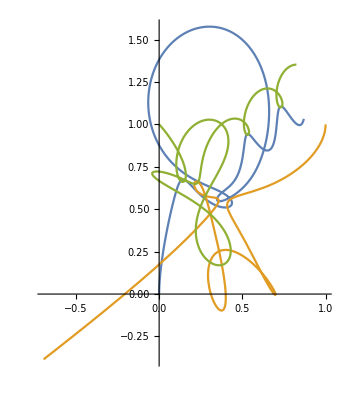

```mathematica
ParametricPlot[Evaluate[%[All,"Position",t]],{t,0,4}]
```

```mathematica
ParametricPlot[Evaluate[%[All,"Position",t]],{t,0,4}]
```

-Graphics-

```mathematica
ParametricPlot[Evaluate[(NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4])[All,"Position",t]],{t,0,4}]
```

-Graphics-

```mathematica
ParametricPlot[Evaluate[(NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4])[All,"Position",t]],{t,0,4}]
```

-Graphics-

```mathematica
Manipulate[
ParametricPlot[
Evaluate[
(NBodySimulation["InverseSquare",{
<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,
<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,
<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4])
[All,"Position",t]],
{t,0,a}],
{a, 1, 10, 1}]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[
(NBodySimulation["InverseSquare",{
<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{0,-1},"Velocity"->{0,0}|>
},4])
[All,"Position",t]],
{t,0,a}],
{a, 1, 10, 1}]
```

```mathematica
data=NBodySimulation["Harmonic",{<|"Mass"->1,"Position"->{-1/3},"Velocity"->{0}|>,<|"Mass"->2,"Position"->{1/3},"Velocity"->{0}|>},10]
```

NBodySimulationData[…]

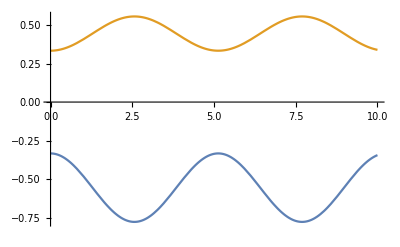

```mathematica
Plot[Evaluate[data[All,"Position",t]],{t,0,10}]
```

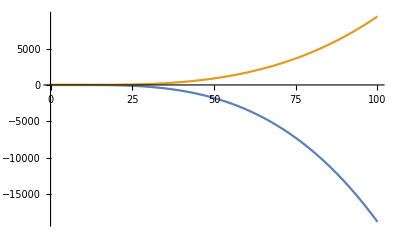

```mathematica
Plot[Evaluate[data[All,"Position",t]],{t,0,100}]
```

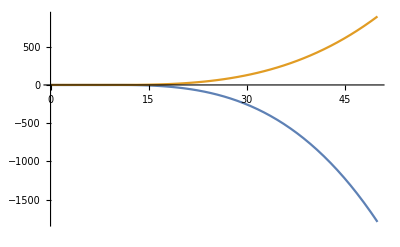

```mathematica
Plot[Evaluate[data[All,"Position",t]],{t,0,50}]
```

```mathematica
Manipulate[
Plot[Evaluate[data[All,"Position",t]],{t,0,a}],
{a, 1, 100}]
```

```mathematica
data[All,4]
```

{<|Mass→1,Position→{-0.514331},Velocity→{0.267441},Momentum→{0.267441}|>,<|Mass→2,Position→{0.423832},Velocity→{-0.133721},Momentum→{-0.267441}|>}

```mathematica
ParametricPlot[Evaluate[data[All,"Position",t]],{t,0,4}]
```

-Graphics-

```mathematica
Manipulate[
ParametricPlot[
Evaluate[
(NBodySimulation["InverseSquare",{
<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{0,-1},"Velocity"->{0,0}|>,
<|"Mass"->1,"Position"->{1,0},"Velocity"->{0,0}|>
},4])
[All,"Position",t]],
{t,0,a}],
{a, 1, 10, 1}]
```

```mathematica
Information[Sin]
```

```mathematica
Information[Classify["NotablePerson"]]
```

Classifier information
Data type | Image
Number of classes | 1001
Method | NotablePerson
Model memory | 904. kB

```mathematica
Information[CloudPut[100!]]
```

CloudObject::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

```mathematica
Information[CloudPut[100!]]
```

CloudObject::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

```mathematica
Information[CloudPut[100!]]
```

CloudConnect::fbdn: Unable to authorize request.  Please contact technical support for assistance.

CloudObject::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.